# ExchPoly - mathematica notebook

This is the mathematica notebook accompanying the article “How Economic Exchange Can Favour Human Genetic Diversity” by Cedric Perret, Luis Santos-Pinto and Laurent Lehmann. You will find here the details of the derivations presented in the article. Please run custom functions before running other parts of the code.

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[StringJoin[$HomeDirectory,"\\OneDrive\\Research\\A1-Projects\\2023_ExchPoly\\res"]];
```

## Custom functions

HL highlights an expression, making the notebook easier to read

```mathematica
Clear[HL]
Options[HL]={"Color"->LightYellow,"FontSize"->18,"Label"->None};
HL[expr_,OptionsPattern[]]:=Module[{styledExpr},styledExpr=If[OptionValue["Label"]===None,HoldForm[expr],(*No label*)Row[{Style[OptionValue["Label"],Bold,Black,FontSize->OptionValue["FontSize"]]," = ",HoldForm[expr]}] (*Add label*)];
Framed[Style[styledExpr,Bold,Black,FontSize->OptionValue["FontSize"]],Background->OptionValue["Color"],FrameStyle->Black,RoundingRadius->5]]
```

Comp compares two expression and print them if the expressions are equals. If a label is provided, the label and the second expressions are printed.

```mathematica
SetAttributes[Comp,HoldAll]
Clear[Comp]
Comp[expr1_,expr2_,label_:None]:=Module[{isEqual,processedExpr1,heldExpr2},(*Extract RHS of rule if expr1 is a list of rules*)If[ListQ[expr1],processedExpr1=expr1[[1]][[1,2]],processedExpr1=expr1];
heldExpr2=HoldForm[expr2];(*preserves input form*)isEqual=TrueQ[Simplify[processedExpr1==expr2]];
If[isEqual===True,If[label===None,HL[heldExpr2,"Label"->expr1],HL[heldExpr2,"Label"->label]],Print[Style["The expressions are NOT equal.",Bold,Red]]]]
```

Examples

```mathematica
Comp[D[x^2,x],2x,"Derivative of x squared"]
Comp[D[x^2,x],5]
```

Derivative of x squared = 2 x

The expressions are NOT equal.

```mathematica
(*Selection gradient *)
Selec[b_]:=Module[{result},
result=D[b,τ]/.{τ->θ}//Simplify;
Print[Style["Selection gradient: ",Orange,Bold,18]];result]
SelecNoPrint[b_]:=D[b,τ]/.{τ->θ}//Simplify;
(*Singular points*)
Singular[b_]:=Module[{result},
result=Flatten[Solve[SelecNoPrint[b]==0,θ]];
Print[Style["Singular point(s): ",Orange,Bold,18]];result]
SingularNoPrint[b_]:=Flatten[Solve[SelecNoPrint[b]==0,θ]];
Singular[b_,var_]:=Module[{result},
result=Flatten[Solve[SelecNoPrint[b]==0,var]];
Print[Style["Singular point(s): ",Orange,Bold,18]];result]
(*Uninvadibility Stability coefficient *)
Invad[b_]:=Module[{result},
result=D[b,{τ,2}]/.{τ->θ};
Print[Style["Heissian - Evolutionary stability: ",Orange,Bold,18]];result]
InvadNoPrint[b_]:=D[b,{τ,2}]/.{τ->θ};
(*Convergence stability coefficient *)
ConvStab[b_]:=Module[{result},
result=D[SelecNoPrint[b],θ];
Print[Style["Jacobian - Convergence stability: ",Orange,Bold,18]];result]
ConvStabNoPrint[b_]:=D[SelecNoPrint[b],θ];
(*Synergy coefficient*)
Synergy[b_]:=Module[{result},
result=D[b,{τ,1},{θ,1}]/.{τ->θ};
Print[Style["Cross-derivative - Neg freq dependent selection: ",Orange,Bold,18]];result]
SynergyNoPrint[b_]:=D[b,{τ,1},{θ,1}]/.{τ->θ};
```

## Production functions (eqs.1)

```mathematica
rx[z_]:=Exp[(-(z-ox)^2)/σ^2]
ry[z_]:=Exp[(-(z-oy)^2)/σ^2]
```

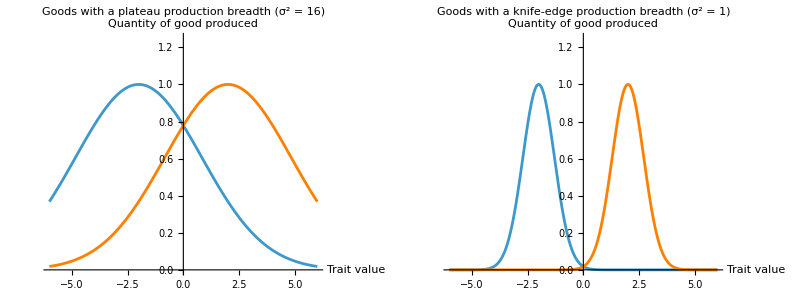

```mathematica
Module[{pox=-2,poy=2,pα1=0.5,pα2 = 0.75,pσ1=4,pσ2=1,bound=6},
ptSigma=Grid[{{Show[Plot[rx[θ]/.{ox->pox,σ->pσ1},{θ,-bound,bound},PlotLabel->Style["Goods with a plateau\nproduction breadth (\!\(\*SuperscriptBox[\(σ\), \(2\)]\) = "<>ToString[pσ1^2]<>")",20],
BaseStyle->{FontSize->14},AxesLabel->{"Trait value","Quantity of good produced "},TicksStyle->{Black,Black},PlotRange->{{-bound,bound},{0,1.25}}],
Plot[ry[θ]/.{oy->poy,σ->pσ1},{θ,-bound,bound},PlotStyle->Orange,Frame->True],ImageSize->Medium],
Show[Plot[rx[θ]/.{ox->pox,σ->pσ2},{θ,-bound,bound},BaseStyle->{FontSize->14},AxesLabel->{"Trait value","Quantity of good produced "},TicksStyle->{Black,Black},PlotRange->{{-bound,bound},{0,1.25}},PlotLabel->Style["Goods with a knife-edge\nproduction breadth (\!\(\*SuperscriptBox[\(σ\), \(2\)]\) = "<>ToString[pσ2]<>")",20]],
Plot[ry[θ]/.{oy->poy,σ->pσ2},{θ,-bound,bound},PlotStyle->Orange],ImageSize->Medium]}}]]
```

```mathematica
Export["pt_sigma.pdf",ptSigma]
```

pt_sigma.pdf

## Behavioural equilibrium

## Autarky - time allocation

Utility function

```mathematica
u[cx_, cy_] := cx^α cy^(1-α)
```

```mathematica
qx[hx_,τ_]:=hx^η rx[τ]
qy[hy_,τ_]:=hy^η ry[τ]
```

```mathematica
HL[Solve[D[u[qx[hx,τ],qy[1-hx,τ]],hx]==0,hx],Label->"Time allocation at equilibrium in autarky"]
```

Time allocation at equilibrium in autarky = {{hx→α}}

## Exchange

```mathematica
Clear[qx,qy,rx,ry,p]
```

```mathematica
(*Remove assumptions applied globally*)
$Assumptions=True;
(*Set assumptions that can be used to simplify expressions*)
myAssumptions =  p>0 &&rx[τ]>0&&ry[τ]>0&&rx[θ]>0&&ry[θ]>0&&0<η<1 && α > 0 ;
SetOptions[Simplify,Assumptions->myAssumptions];
SetOptions[FullSimplify,Assumptions->myAssumptions];
(*Silence warnings from Solve about inverse functions*)
Off[Solve::ifun]
```

Utility Function

```mathematica
u[cx_, cy_] := cx^α cy^(1-α)
```

Lagrangian

```mathematica
L[cx_,cy_,hx_,λ_,δ_,τ_]:=u[cx,cy]-λ(p cx +  cy-p qx[hx,τ]- qy[1-hx,τ]  )
```

Test for concavity of Lagrangian

```mathematica
Eigenvalues[D[L[cx,cy,hx,λ,δ,τ],{{cx,cy,hx},2}]]//MatrixForm
```

(0
cx^(-2+α) cy^(-1-α) (cx^2+cy^2) (-1+α) α
λ (p qx^(2,0)[hx,τ]+qy^(2,0)[1-hx,τ]))

All negative if the production functions are concave, that is if η < 1

```mathematica
Quantities consumed
```

```mathematica
Comp[(D[L[cx1,cy1,hx1,λ1,δ1,τ],cx1]),α cx1^(α-1)cy1^(1-α)-λ1 p,"δL/δcx1"]
Comp[(D[L[cx1,cy1,hx1,λ1,δ1,τ],cy1]),(1-α) cx1^α cy1^-α-λ1 ,"δL/δcy1"]
```

δL/δcx1 = α cx1^(α-1) cy1^(1-α)-λ1 p

δL/δcy1 = (1-α) cx1^α cy1^-α-λ1

```mathematica
Comp[Solve[(α cx1^(α-1)cy1^(1-α))/((1-α) cx1^α cy1^-α)==(λ1 p)/λ1,cy1], (1-α)/α  p/1 cx1,"cy(cx)"]//Simplify
```

cy(cx) = ((1-α) p cx1)/α

```mathematica
Comp[Solve[(p qx[hx1,τ]+ qy[1-hx1,τ]-p cx1 - cy1 /.{cy1->(1-α)/α  p cx1})==0,cx1],α (qx[hx1,τ]+ qy[1-hx1,τ] 1/p),Subscript[Overscript["c","^"],"x"]]
```

(ĉ)_x = α (qx[hx1,τ]+qy[1-hx1,τ]/p)

```mathematica
Comp[((1-α)/α  p cx1 /.{cx1->α (qx[hx1,τ]+ qy[1-hx1,τ] 1/p)}),(1-α) (p qx[hx1,τ]+qy[1-hx1,τ]),Subscript[Overscript["c","^"],"y"]]
```

(ĉ)_y = (1-α) (p qx[hx1,τ]+qy[1-hx1,τ])

Time allocations

```mathematica
Comp[D[L[cx1,cy1,hx1,λ1,δ1,τ],hx1],λ1 (p Derivative[1,0][qx][hx1,τ]-Derivative[1,0][qy][1-hx1,τ]),"δL/δhx1"]
```

δL/δhx1 = λ1 (p qx^(1,0)[hx1,τ]-qy^(1,0)[1-hx1,τ])

To go further, we need to specify the functions determining productions

```mathematica
qx[hx_,τ_]:=hx^η rx[τ]
qy[hy_,τ_]:=hy^η ry[τ]
```

```mathematica
Comp[(p Derivative[1,0][qx][hx1,τ]-Derivative[1,0][qy][1-hx1,τ]),p η hx1^(η-1)  rx[τ]-η(1-hx1)^(η-1)  ry[τ],"δL/δhx1"]
```

δL/δhx1 = p η hx1^(η-1) rx[τ]-η (1-hx1)^(η-1) ry[τ]

Demonstration that the solution found in the manuscript is the right one

```mathematica
(Derivative[1,0][qy][1-hx1,τ]/Derivative[1,0][qx][hx1,τ])/.{hx1->1/(1+(1/p ry[τ]/rx[τ])^(1/(1-η)))}//FullSimplify
```

p

Thus,

```mathematica
HL[1/(1+(1/p ry[τ]/rx[τ])^(1/(1-η))),Label->Subscript[Overscript["h","^"],"x1"]]
```

(ĥ)_x1 = 1/(1+(ry[τ]/(p rx[τ]))^(1/(1-η)))

#### Price p

We give here the example of dyadic exchange which can easily be extended to a market with N players.

```mathematica
Comp[Solve[cx1+cx2==qx[hx1,τ]+qx[hx2,θ]/.{cx1->α (qx[hx1,τ]+ qy[1-hx1,τ] 1/p),cx2->α (qx[hx2,θ]+ qy[1-hx2,θ] 1/p)},p],(α(qy[1-hx2,θ]+qy[1-hx1,τ]))/((1-α)(qx[hx2,θ]+qx[hx1,τ])),"Price p"]
```

Price p = (α (qy[1-hx2,θ]+qy[1-hx1,τ]))/((1-α) (qx[hx2,θ]+qx[hx1,τ]))

We now give an example on how the price and behavioural equilibria can be determined numerically.

Numerical analysis

Set values for parameters

```mathematica
subs={T->1,py->1,η->0.5,rx[τ]->0.001,ry[τ]->1,rx[θ]->0.001,ry[θ]->1,α->0.5,px->p};
subs={T->1,py->1,η->0.5,rx[τ]->1,ry[τ]->0.8,rx[θ]->0.9,ry[θ]->0.97,α->0.5,px->p};
```

Price

```mathematica
psub=FindRoot[(p==(α(qy[1-hx2,θ]+qy[1-hx1,τ]))/((1-α)(qx[hx2,θ]+qx[hx1,τ])))/.{hx1->1/(1+(1/p ry[τ]/rx[τ])^(1/(1-η))),hx2->1/(1+(1/p ry[θ]/rx[θ])^(1/(1-η)))}/.subs,{p,0.2}]
```

{p→0.931596}

Time allocations

```mathematica
hsub={hx1->1/(1+(1/p ry[τ]/rx[τ])^(1/(1-η))),hx2->1/(1+(1/p ry[θ]/rx[θ])^(1/(1-η)))}/.subs/.psub
```

{hx1→0.57556,hx2→0.427633}

Quantities consumed - Player 1

```mathematica
α (qx[hx1,τ]+ qy[1-hx1,τ] 1/p)/.subs/.psub/.hsub
```

0.659059

Quantities consumed - Player 2

```mathematica
(1-α) (p qx[hx1,τ]+qy[1-hx1,τ])/.subs/.psub/.hsub
```

0.613977

#### A unique price

We now demonstrate that there is a single unique price, meaning that there is a single solution to the equation solved for the price.

First, the price is always decreasing if the expressions in brown are positive.

```mathematica
Clear[qx,qy,hx,hy,rx,ry]
```

```mathematica
Comp[D[α/(1-α)qy[h[p],θ]/qx[h[p],θ]-p,p]//FullSimplify,-1+α/(1-α)(h'[p] (qx[h[p],θ] Derivative[1,0][qy][h[p],θ]-qy[h[p],θ] Derivative[1,0][qx][h[p],θ]))/qx[h[p],θ]^2,"Derivative of f[p] (see appendix)"]
```

Derivative of f[p] (see appendix) = -1+(α (h'[p] (qx[h[p],θ] qy^(1,0)[h[p],θ]-qy[h[p],θ] qx^(1,0)[h[p],θ])))/((1-α) qx[h[p],θ]^2)

This is true if the derivative of hx with respect to price are positive too.

```mathematica
D[1/(1+(1/p ry[τ]/rx[τ])^(1/(1-η))),p]//Simplify;
Comp[%,((1 ry[τ])/(p rx[τ]))^(1/(1-η))/(p (1-η) (1+((1 ry[τ])/(p rx[τ]))^(1/(1-η)))^2)//Simplify,"Derivative of h(p)"]
```

Derivative of h(p) = Simplify[(ry[τ]/(p rx[τ]))^(1/(1-η))/(p (1-η) (1+(ry[τ]/(p rx[τ]))^(1/(1-η)))^2)]

#### Time allocation with market exchange and monomorphic population

```mathematica
qx[hx_,τ_]:=hx^η rx[τ]
qy[hy_,τ_]:=hy^η ry[τ]
```

Using the value of h we derived in the main text and replacing the price for a monomorphic population, the time allocation of a resident reduces to

```mathematica
1/(1+(1/p ry[θ]/rx[θ])^(1/(1-η)))/.{p->(α qy[1-hx1,θ])/((1-α)qx[hx1,θ])}/.{hx1->α}//Simplify
```

α

The time allocation of a mutant individual is

```mathematica
1/(1+(1/p ry[τ]/rx[τ])^(1/(1-η)))/.{p->(α qy[1-hx1,θ])/((1-α)qx[hx1,θ])}/.{hx1->α}//Simplify
```

1/(1+(-1+1/α) ((rx[θ] ry[τ])/(rx[τ] ry[θ]))^(1/(1-η)))

## Evolutionary analysis with time allocation fixed

## Autarky

```mathematica
Utility and invasion payoff
```

```mathematica
(*Utility function*)
Π[cx_,cy_]:=cx^α cy^(1-α)
(*Invasion payoff of an individual τ in a resident monomorphic population  of trait θ*) 
paNoEx[τ_,θ_]:=Π[qx[τ],qy[τ]]
```

```mathematica
General analysis  (qx, qy and p unspecified)
```

```mathematica
Clear[qx,qy]
```

```mathematica
Comp[SelecNoPrint[paNoEx[τ,θ]] , qx[θ]^(-1+α) qy[θ]^-α (α qy[θ] qx'[θ]+(1-α) qx[θ] qy'[θ]),"Selection gradient"]
```

Selection gradient = qx[θ]^(-1+α) qy[θ]^-α (α qy[θ] qx'[θ]+(1-α) qx[θ] qy'[θ])

```mathematica
SingSub=Singular[paNoEx[τ,θ],qy'[θ]]
```

Singular point(s):

{qy'[θ]→(α qy[θ] qx'[θ])/((-1+α) qx[θ])}

```mathematica
ConvStab[paNoEx[τ,θ]]/.SingSub//Simplify
```

Jacobian - Convergence stability:

(qx[θ]^(-2+α) qy[θ]^-α (α qy[θ] (qx'[θ]^2+(-1+α) qx[θ] qx''[θ])-(-1+α)^2 qx[θ]^2 qy''[θ]))/(-1+α)

```mathematica
Synergy[paNoEx[τ,θ]]/.SingSub//Simplify
```

Cross-derivative - Neg freq dependent selection:

0

```mathematica
Invad[paNoEx[τ,θ]]/.SingSub//Simplify
```

Heissian - Evolutionary stability:

(qx[θ]^(-2+α) qy[θ]^-α (α qy[θ] (qx'[θ]^2+(-1+α) qx[θ] qx''[θ])-(-1+α)^2 qx[θ]^2 qy''[θ]))/(-1+α)

```mathematica
InvadNoPrint[paNoEx[τ,θ]]==ConvStabNoPrint[paNoEx[τ,θ]]//Simplify
```

True

```mathematica
Analysis with defined production functions
```

```mathematica
qx[z_]:=Exp[(-(z-ox)^2)/σ^2]
qy[z_]:=Exp[(-(z-oy)^2)/σ^2]
```

```mathematica
Selec[paNoEx[τ,θ]]//FullSimplify
```

Selection gradient:

-(2 (ⅇ^(-(ox-θ)^2/σ^2))^α (ⅇ^(-(oy-θ)^2/σ^2))^(1-α) (oy (-1+α)-ox α+θ))/σ^2

```mathematica
Singular[paNoEx[τ,θ],θ]//FullSimplify
```

Singular point(s):

{θ→oy+ox α-oy α}

```mathematica
ConvStab[paNoEx[τ,θ]]/.{θ->oy+ox α-oy α}//Simplify
```

Jacobian - Convergence stability:

-(2 (ⅇ^(-((ox-oy)^2 (-1+α)^2)/σ^2))^α (ⅇ^(-((ox-oy)^2 α^2)/σ^2))^(1-α))/σ^2

We have shown in the analysis with unspecified qx, qy and p, that the synergy coefficient is always 0, and the invasibility coefficient is equal to the convergence coefficient

## Dyadic exchange

```mathematica
Utility and invasion payoff
```

```mathematica
Π[cx_,cy_]:=cx^α cy^(1-α)
cx[τ_,θ_]:=(α (p[τ,θ] qx[τ]+qy[τ]))/p[τ,θ]
cy[τ_,θ_]:=(1-α) (p[τ,θ] qx[τ]+qy[τ]) 
pa[τ_,θ_]:=Π[cx[τ,θ],cy[τ,θ]]
```

```mathematica
General analysis (qx, qy, and p unspecified)
```

```mathematica
Clear[qx,qy,p]
```

```mathematica
Comp[SelecNoPrint[pa[τ,θ]] , ((((1-α) (p[θ,θ] qx[θ]+qy[θ])))^-α (α (qx[θ]+qy[θ]/p[θ,θ]))^α)/1(1-α)*  (p[θ,θ] qx'[θ]+qy'[θ]-Derivative[1,0][p][θ,θ]((α qy[θ]*(1/p[θ,θ]))-(1-α)  qx[θ])),"Selection gradient"]
```

Selection gradient = (((1-α) (p[θ,θ] qx[θ]+qy[θ]))^-α (α (qx[θ]+qy[θ]/p[θ,θ]))^α) (1-α) (p[θ,θ] qx'[θ]+qy'[θ]-p^(1,0)[θ,θ] ((α qy[θ])/p[θ,θ]-(1-α) qx[θ]))

```mathematica
General analysis with price defined (only qx, qy unspecified)
```

```mathematica
p[τ_,θ_]:=(α (qy[τ]+qy[θ]))/((1-α) (qx[τ]+qx[θ]))
cx[τ,θ]==α*qx[τ] + (1-α)*qy[τ]*(qx[τ]+qx[θ])/(qy[τ]+qy[θ])//FullSimplify
cy[τ,θ]==(1-α)*qy[τ] + α*qx[τ]*(qy[τ]+qy[θ])/(qx[τ]+qx[θ])//FullSimplify
```

True

True

```mathematica
SelecNoPrint[pa[τ,θ]]==SelecNoPrint[paNoEx[τ,θ]]//FullSimplify
```

True

Selection gradient simplifies to the one in autarky without exchange

Thus, the singular point and convergence coefficient are the same than in autarky

```mathematica
SingSub=Singular[pa[τ,θ],qy'[θ]]
```

Singular point(s):

{qy'[θ]→(α qy[θ] qx'[θ])/((-1+α) qx[θ])}

```mathematica
Synergy[pa[τ,θ]]/.SingSub//Simplify
```

Cross-derivative - Neg freq dependent selection:

(α qx[θ]^(-2+α) qy[θ]^(1-α) qx'[θ]^2)/(4 (-1+α))

This expression is always negative

```mathematica
Comp[InvadNoPrint[pa[τ,θ]]/.SingSub//Simplify,qx[θ]^(-1+α) qy[θ]^-α ((  α qy[θ]qx''[θ]+(1-α) qx[θ] qy''[θ])- (3/4) α/(1-α) qy[θ]/qx[θ] qx'[θ]^2),"Uninvadibility coefficient"]
```

Uninvadibility coefficient = qx[θ]^(-1+α) qy[θ]^-α ((α qy[θ] qx''[θ]+(1-α) qx[θ] qy''[θ])-(3 α qy[θ] qx'[θ]^2)/(4 (1-α) qx[θ]))

Using the condition found earlier defining the singular point

```mathematica
SingSub=Singular[pa[τ,θ],qx'[θ]]
```

Singular point(s):

{qx'[θ]→((-1+α) qx[θ] qy'[θ])/(α qy[θ])}

Substituting one of the partial derivative by this expression gives

```mathematica
Comp[qx[θ]^(-1+α) qy[θ]^-α ((  α qy[θ]qx''[θ]+(1-α) qx[θ] qy''[θ])- (3/4) α/(1-α) qy[θ]/qx[θ] qx'[θ](((-1+α) qx[θ] qy'[θ])/(α qy[θ]))),qx[θ]^(-1+α) qy[θ]^-α ((  α qy[θ]qx''[θ]+(1-α) qx[θ] qy''[θ])+ (3/4) qx'[θ]qy'[θ])]
```

qx[θ]^(-1+α) qy[θ]^-α (-(3 (-1+α) qx'[θ] qy'[θ])/(4 (1-α))+α qy[θ] qx''[θ]+(1-α) qx[θ] qy''[θ]) = qx[θ]^(-1+α) qy[θ]^-α ((α qy[θ] qx''[θ]+(1-α) qx[θ] qy''[θ])+3/4 qx'[θ] qy'[θ])

This expression is positive if

```mathematica
HL[α qy[θ]qx''[θ]+(1-α) qx[θ] qy''[θ]+ (3/4) qx'[θ]qy'[θ]>0,Label->"Conditions for positive uninvadibility coefficient in dyadic exchange"]
```

Conditions for positive uninvadibility coefficient in dyadic exchange = 3/4 qx'[θ] qy'[θ]+α qy[θ] qx''[θ]+(1-α) qx[θ] qy''[θ]>0

```mathematica
Analysis with defined production functions
```

```mathematica
qx[z_]:=Exp[(-(z-ox)^2)/σ^2]
qy[z_]:=Exp[(-(z-oy)^2)/σ^2]
```

```mathematica
Singular[pa[τ,θ],θ]
```

Singular point(s):

{θ→oy+ox α-oy α}

```mathematica
Invad[pa[τ,θ]]/.{θ->oy+ox α-oy α}//Simplify
```

Heissian - Evolutionary stability:

-((ⅇ^(-((ox-oy)^2 (-1+α)^2)/σ^2))^α (ⅇ^(-((ox-oy)^2 α^2)/σ^2))^(1-α) (ox^2 (-1+α) α-2 ox oy (-1+α) α+oy^2 (-1+α) α+2 σ^2))/σ^4

Coefficient is positive if the following expression is negative

```mathematica
(ox^2 (-1+α) α-2 ox oy (-1+α) α+oy^2 (-1+α) α+2 σ^2)//FullSimplify
```

(ox-oy)^2 (-1+α) α+2 σ^2

```mathematica
HL[(ox-oy)^2/σ^2>2/(α(1-α)),Label->"Conditions for positive uninvadibility coefficient in dyadic exchange"]
```

Conditions for positive uninvadibility coefficient in dyadic exchange = (ox-oy)^2/σ^2>2/((1-α) α)

## Market exchange

```mathematica
Utility and invasion payoff
```

```mathematica
Clear[p,qx,qy]
```

```mathematica
Π[cx_,cy_]:=cx^α cy^(1-α)
cx[τ_,θ_]:=(α (p[τ,θ] qx[τ]+qy[τ]))/p[τ,θ]
cy[τ_,θ_]:=(1-α) (p[τ,θ] qx[τ]+qy[τ])
p[τ_,θ_]:=(α (qy[θ]))/((1-α) (qx[θ]))
(*Invasion payoff of an individual τ in a resident monomorphic population  of trait θ*) 
paMarket[τ_,θ_]:=Π[cx[τ,θ],cy[τ,θ]]
```

```mathematica
Selec[paMarket[τ,θ]]
```

Selection gradient:

qx[θ]^(-1+α) qy[θ]^-α (α qy[θ] qx'[θ]-(-1+α) qx[θ] qy'[θ])

Selection gradient simplifies to the one in autarky without exchange

```mathematica
SelecNoPrint[paMarket[τ,θ]]==SelecNoPrint[paNoEx[τ,θ]]//FullSimplify
```

True

Thus, the singular point and convergence coefficient are the same than in autarky

```mathematica
SingSub=Singular[paMarket[τ,θ],qy'[θ]]
```

Singular point(s):

{qy'[θ]→(α qy[θ] qx'[θ])/((-1+α) qx[θ])}

```mathematica
Comp[SynergyNoPrint[paMarket[τ,θ]]/.SingSub,-qx[θ]^(-2+α) qy[θ]^(1-α)α/(1-α)qx'[θ]^2,"Cross-derivative"]
```

Cross-derivative = -(qx[θ]^(-2+α) qy[θ]^(1-α) α qx'[θ]^2)/(1-α)

Always negative

```mathematica
Invad[paMarket[τ,θ]]/.SingSub//Simplify
```

Heissian - Evolutionary stability:

qx[θ]^(-1+α) qy[θ]^-α (α qy[θ] qx''[θ]-(-1+α) qx[θ] qy''[θ])

```mathematica
HL[α qy[θ] qx''[θ]-(-1+α) qx[θ] qy''[θ]>0,Label->"Conditions for positive uninvadibility coefficient in market exchange"]
```

Conditions for positive uninvadibility coefficient in market exchange = α qy[θ] qx''[θ]-(-1+α) qx[θ] qy''[θ]>0

```mathematica
Analysis with defined production functions
```

```mathematica
qx[z_]:=Exp[(-(z-ox)^2)/σ^2]
qy[z_]:=Exp[(-(z-oy)^2)/σ^2]
```

```mathematica
Singular[paMarket[τ,θ]]
```

Singular point(s):

{θ→oy+ox α-oy α}

```mathematica
Invad[paMarket[τ,θ]]/.{θ->oy+ox α-oy α}//Simplify
```

Heissian - Evolutionary stability:

-(2 (ⅇ^(-((ox-oy)^2 (-1+α)^2)/σ^2))^α (ⅇ^(-((ox-oy)^2 α^2)/σ^2))^(1-α) (2 ox^2 (-1+α) α-4 ox oy (-1+α) α+2 oy^2 (-1+α) α+σ^2))/σ^4

This expression is positive if the following expression is negative

```mathematica
(2 ox^2 (-1+α) α-4 ox oy (-1+α) α+2 oy^2 (-1+α) α+σ^2)//FullSimplify
```

2 (ox-oy)^2 (-1+α) α+σ^2

```mathematica
HL[(ox-oy)^2/σ^2>1/(2α(1-α)) ,Label->"Conditions for positive uninvadibility coefficient in market exchange"]
```

Conditions for positive uninvadibility coefficient in market exchange = (ox-oy)^2/σ^2>1/(2 (1-α) α)

## Evolutionary analysis with time allocation decision

## Autarky

```mathematica
(*Remove assumptions previously applied globally*)
$Assumptions=True;
(*Set assumptions that can be used to simplify expressions*)
myAssumptions =  p>0 &&rx[τ]>0&&ry[τ]>0&&rx[θ]>0&&ry[θ]>0&&0<η<1 && 0 <α < 1  ;
SetOptions[Simplify,Assumptions->myAssumptions];
SetOptions[FullSimplify,Assumptions->myAssumptions];
(*Silence warnings from Solve about inverse functions*)
Off[Solve::ifun]
```

### Utility and mutant payoff

```mathematica
Clear[paNoEx,qx,qy,rx,ry]
```

```mathematica
(*Utility function*)
Π[cx_,cy_]:=cx^α cy^(1-α)
(*Invasion payoff of an individual τ in a resident monomorphic population  of trait θ*) 
paNoEx[τ_,θ_]:=Π[qx[α,τ],qy[1-α,τ]]
```

```mathematica
qx[hx_,τ_]:=hx^η rx[τ]
qy[hy_,τ_]:=hy^η ry[τ] 
rx[z_]:=Exp[(-(z-ox)^2)/σ^2]
ry[z_]:=Exp[(-(z-oy)^2)/σ^2]
```

```mathematica
PowerExpand[Selec[paNoEx[τ,θ]]//FullSimplify]
Comp[%,(2 ⅇ^(-((α (ox-θ)^2+(1-α) (oy-θ)^2)/σ^2)) (1-α)^((1-α) η) α^(α η) (α ox + (1-α) oy-θ))/σ^2,"Selection gradient"]
```

Selection gradient:

(2 ⅇ^(-(α (ox-θ)^2)/σ^2-((1-α) (oy-θ)^2)/σ^2) (1-α)^(η-α η) α^(α η) (oy+ox α-oy α-θ))/σ^2

Selection gradient = (2 ⅇ^(-(α (ox-θ)^2+(1-α) (oy-θ)^2)/σ^2) (1-α)^((1-α) η) α^(α η) (α ox+(1-α) oy-θ))/σ^2

```mathematica
Singular[paNoEx[τ,θ]]//Simplify
singularPtSub=SingularNoPrint[paNoEx[τ,θ]][[1]];
```

Singular point(s):

{θ→oy+ox α-oy α,θ→ox+σ (-∞),θ→ox+σ ∞}

```mathematica
ConvStab[paNoEx[τ,θ]]/.singularPtSub//Simplify;
Comp[%,-(2(ⅇ^(-((ox-oy)^2 (1-α)^2)/σ^2) α^η)^α (ⅇ^(-((ox-oy)^2 α^2)/σ^2) (1-α)^η)^(1-α))/σ^2,"Convergence coefficient"]
```

Jacobian - Convergence stability:

Convergence coefficient = -(2 (ⅇ^(-((ox-oy)^2 (1-α)^2)/σ^2) α^η)^α (ⅇ^(-((ox-oy)^2 α^2)/σ^2) (1-α)^η)^(1-α))/σ^2

```mathematica
Synergy[paNoEx[τ,θ]]/.singularPtSub//Simplify
```

Cross-derivative - Neg freq dependent selection:

0

```mathematica
Invad[paNoEx[τ,θ]]/.singularPtSub//Simplify;
Comp[%,-(2(ⅇ^(-((ox-oy)^2 (1-α)^2)/σ^2) α^η)^α (ⅇ^(-((ox-oy)^2 α^2)/σ^2) (1-α)^η)^(1-α))/σ^2,"Uninvadibility coefficient"]
```

Heissian - Evolutionary stability:

Uninvadibility coefficient = -(2 (ⅇ^(-((ox-oy)^2 (1-α)^2)/σ^2) α^η)^α (ⅇ^(-((ox-oy)^2 α^2)/σ^2) (1-α)^η)^(1-α))/σ^2

Always negative

## Dyadic exchange

```mathematica
(*Remove previous assumptions*)
$Assumptions=True;
(*Set assumptions that can be used to simplify expressions*)
myAssumptions =  p>0 &&rx[τ]>0&&ry[τ]>0&&rx[θ]>0&&ry[θ]>0&&0<η<1 && 0 <α < 1  ;
SetOptions[Simplify,Assumptions->myAssumptions];
SetOptions[FullSimplify,Assumptions->myAssumptions];
(*Silence warnings from Solve about inverse functions*)
Off[Solve::ifun]
```

### Utility and mutant payoff

```mathematica
Clear[p]
```

```mathematica
(*Utility function*)
Π[cx_,cy_]:=cx^α cy^(1-α)
(*Invasion payoff of an individual τ in a resident monomorphic population  of trait θ*) 
paEconDiminishing[τ_,θ_]:=Π[cx[τ,θ],cy[τ,θ]]
```

We use a price that we will compute numerically, as done in the behavioural equilibrium section

```mathematica
cx[τ_,θ_]:=α (qx[hx[τ,p[τ,θ]],τ]+ qy[1-hx[τ,p[τ,θ]],τ] 1/p[τ,θ])/.{p[τ,θ]->pNum[τ,θ,η,ox,oy,σ]}
cy[τ_,θ_]:= (1-α)(p[τ,θ]qx[hx[τ,p[τ,θ]],τ]+ qy[1-hx[τ,p[τ,θ]],τ])/.{p[τ,θ]->pNum[τ,θ,η,ox,oy,σ]}
```

```mathematica
qx[hx_,τ_]:=hx^η rx[τ]
qy[hy_,τ_]:=hy^η ry[τ]
```

```mathematica
hx[τ_,p_]:=1/(1+(1/p ry[τ]/rx[τ])^(1/(1-η)))
```

```mathematica
rx[z_]:=Exp[(-(z-ox)^2)/σ^2]
ry[z_]:=Exp[(-(z-oy)^2)/σ^2]
```

We derive the expression to solve to get the price numerically. We substitute the values of parameters that are already set

```mathematica
p==(α(qy[1-hx[θ,p],θ]+qy[1-hx[τ,p],τ]))/((1-α)(qx[hx[θ,p],θ]+qx[hx[τ,p],τ]))/.{ox->-2,oy->2,α->0.5}//PowerExpand//Simplify
```

p==(1. ⅇ^((8 (θ+τ))/σ^2) (1+ⅇ^(-(8 θ)/((-1+η) σ^2)) p^(1/(-1+η)))^η (1+ⅇ^(-(8 τ)/((-1+η) σ^2)) p^(1/(-1+η)))^η (ⅇ^((-2+τ)^2/σ^2) (1-1/(1+ⅇ^(-(8 θ)/((-1+η) σ^2)) p^(1/(-1+η))))^η+ⅇ^((-2+θ)^2/σ^2) (1-1/(1+ⅇ^(-(8 τ)/((-1+η) σ^2)) p^(1/(-1+η))))^η))/(ⅇ^((2+θ)^2/σ^2) (1+ⅇ^(-(8 θ)/((-1+η) σ^2)) p^(1/(-1+η)))^η+ⅇ^((2+τ)^2/σ^2) (1+ⅇ^(-(8 τ)/((-1+η) σ^2)) p^(1/(-1+η)))^η)

Numerical expression for price

```mathematica
Clear[pNum]
```

```mathematica
pNum[τ_?NumericQ,θ_?NumericQ,η_?NumericQ,ox_?NumericQ,oy_?NumericQ,σ_?NumericQ]:=pNum[τ?NumericQ,θ?NumericQ,η?NumericQ,ox?NumericQ,oy?NumericQ,σ?NumericQ]=p/.FindRoot[p==(1. ⅇ^((8 (θ+τ))/σ^2) (1+ⅇ^(-(8 θ)/((-1+η) σ^2)) p^(1/(-1+η)))^η (1+ⅇ^(-(8 τ)/((-1+η) σ^2)) p^(1/(-1+η)))^η (ⅇ^((-2+τ)^2/σ^2) (1-1/(1+ⅇ^(-(8 θ)/((-1+η) σ^2)) p^(1/(-1+η))))^η+ⅇ^((-2+θ)^2/σ^2) (1-1/(1+ⅇ^(-(8 τ)/((-1+η) σ^2)) p^(1/(-1+η))))^η))/(ⅇ^((2+θ)^2/σ^2) (1+ⅇ^(-(8 θ)/((-1+η) σ^2)) p^(1/(-1+η)))^η+ⅇ^((2+τ)^2/σ^2) (1+ⅇ^(-(8 τ)/((-1+η) σ^2)) p^(1/(-1+η)))^η),{p,0.2}]
```

```mathematica
pNum[0.,0.22,0.5,-2,2,1]
```

2.35662

We define the derivative of price with respect to traits using manual finite difference methods to conduct analysis (ND is much more computationally expensive and we do not need that much precision)

```mathematica
(*Memoization: Apparaently a trick so that it remembers in memory when the function is called once (useful as we don't want it to compute and find h multiple times for each derivative*)
(*https://reference.wolfram.com/language/workflow/WriteAFunctionThatRemembersComputedValues.html*)
```

```mathematica
Needs["NumericalCalculus`"]
Derivative[1,0,0,0,0,0][pNum][τ_,θ_,η_,ox_,oy_,σ_]:=(pNum[τ+0.000001,θ,η,ox,oy,σ]-pNum[τ,θ,η,ox,oy,σ])/(0.000001);
Derivative[2,0,0,0,0,0][pNum][τ_,θ_,η_,ox_,oy_,σ_]:=(D[pNum[τ+0.000001,θ,η,ox,oy,σ],{τ,1}]-D[pNum[τ,θ,η,ox,oy,σ],{τ,1}])/(0.000001);
Derivative[0,1,0,0,0,0][pNum][τ_,θ_,η_,ox_,oy_,σ_]:=(pNum[τ,θ+0.000001,η,ox,oy,σ]-pNum[τ,θ,η,ox,oy,σ])/(0.000001);
Derivative[0,2,0,0,0,0][pNum][τ_,θ_,η_,ox_,oy_,σ_]:=(D[pNum[τ,θ+0.000001,η,ox,oy,σ],{θ,1}]-D[pNum[τ,θ,η,ox,oy,σ],{θ,1}])/(0.000001);
Derivative[1,1,0,0,0,0][pNum][τ_,θ_,η_,ox_,oy_,σ_]:=ND[pNum[τ,θ,η,ox,oy,σ],{τ,1},{θ,1}];
```

We examine the singular point and different coefficients numerically on the range of parameters considered

```mathematica
EvolEqNumericalDiminishing[pα_,pη_,pox_,poy_,pσ_]:=Block[{ α=pα,η=pη,ox=pox,oy=poy,σ=pσ},
Eq=θ/.FindRoot[(D[paEconDiminishing[τ,θ],τ]==0)/.{τ->θ},{θ,0.}]
]
EvolEqNumericalDiminishing[0.5,0.5,-2,2,0.5]
```

0.

```mathematica
AllTrue[Flatten[Table[EvolEqNumericalDiminishing[0.5,pη,-2,2,Sqrt[pσ]],{pη,0.0,0.95,0.05},{pσ,1,20,1}]],#==0&]
```

True

0 is a singular point on the range of parameters considered.

```mathematica
ConvergenceNumericalDiminishing[pα_,pη_,pox_,poy_,pσ_,ppPoint_]:=Block[{ α=pα,η=pη,ox=pox,oy=poy,σ=pσ,pPoint=ppPoint},
D[(D[paEconDiminishing[τ,θ],τ]/.{τ->θ}),θ]/.{θ->pPoint}
]
ConvergenceNumericalDiminishing[0.5,0.5,-2,2,3,0]
```

-0.100752

```mathematica
AllTrue[Flatten[Table[ConvergenceNumericalDiminishing[0.5,pη,-2,2,Sqrt[pσ],0],{pη,0.0,0.95,0.05},{pσ,1,20,1}]],#<0&]
```

True

0 is convergent on the range of parameters considered

```mathematica
InvadNumericalDiminishing[pα_,pη_,pox_,poy_,pσ_,ppPoint_]:=Block[{ α=pα,η=pη,ox=pox,oy=poy,σ=pσ,pPoint=ppPoint},
Re[D[paEconDiminishing[τ,θ],{τ,2}]/.{τ->θ}/.{θ->pPoint}]
]
InvadNumericalDiminishing[0.5,0.7,-2,2,3,0]
```

-0.0227395

We find directly the value above which the uninvadability coefficient is positive for each value of η

```mathematica
limitInvadRaw=Table[{pη,(x/.ResourceFunction["BisectionMethodFindRoot"][InvadNumericalDiminishing[0.5,pη,-2,2,Sqrt[x],0],{x,1,20},5,100])},{pη,0.,0.95,0.05}]
```

{{0.,2.},{0.05,2.1053},{0.1,2.2223},{0.15,2.3529},{0.2,2.5},{0.25,2.6667},{0.3,2.8572},{0.35,3.0769},{0.4,3.3334},{0.45,3.6363},{0.5,4.},{0.55,4.4444},{0.6,5.0001},{0.65,5.7143},{0.7,6.6666},{0.75,7.9999},{0.8,10.},{0.85,13.333},{0.9,20.},{0.95,20.}}

```mathematica
limitInvad=Reverse[limitInvadRaw,2];
limitInvad=Prepend[limitInvad,{0,0}];
limitInvad=Prepend[limitInvad,{0,0.99}];
limitInvad=Append[limitInvad,{0,0.99}]
```

{{0,0.99},{0,0},{2.,0.},{2.1053,0.05},{2.2223,0.1},{2.3529,0.15},{2.5,0.2},{2.6667,0.25},{2.8572,0.3},{3.0769,0.35},{3.3334,0.4},{3.6363,0.45},{4.,0.5},{4.4444,0.55},{5.0001,0.6},{5.7143,0.65},{6.6666,0.7},{7.9999,0.75},{10.,0.8},{13.333,0.85},{20.,0.9},{20.,0.95},{0,0.99}}

This is simply a copy from the results before. It is to avoid recomputing all the results if changes on the plot are required.

```mathematica
limitInvad={{0,0.99},{0,0},{2.00000762939453125`5.,0.},{2.10524749755859375`5.,0.05},{2.22220611572265625`5.,0.1},{2.3529205322265625`5.,0.15000000000000002},{2.4999542236328125`5.,0.2},{2.6666717529296875`5.,0.25},{2.8571014404296875`5.,0.30000000000000004},{3.0769195556640625`5.,0.35000000000000003},{3.3333587646484375`5.,0.4},{3.6364898681640625`5.,0.45},{3.9998626708984375`5.,0.5},{4.4444427490234375`5.,0.55},{5.000030517578125`5.,0.6000000000000001},{5.714324951171875`5.,0.65},{6.666656494140625`5.,0.7000000000000001},{8.000030517578125`5.,0.75},{9.99981689453125`5.,0.8},{13.33343505859375`5.,0.8500000000000001},{20.0001220703125`5.,0.9},{24.9996337890625`5.,0.9500000000000001},{0,0.99}}
```

{{0,0.99},{0,0},{2.,0.},{2.1052,0.05},{2.2222,0.1},{2.3529,0.15},{2.5,0.2},{2.6667,0.25},{2.8571,0.3},{3.0769,0.35},{3.3334,0.4},{3.6365,0.45},{3.9999,0.5},{4.4444,0.55},{5.,0.6},{5.7143,0.65},{6.6667,0.7},{8.,0.75},{9.9998,0.8},{13.333,0.85},{20.,0.9},{25.,0.95},{0,0.99}}

```mathematica
maxSigmaSquare =20 ;
```

```mathematica
limitInvad=limitInvad/. {x_,y_}/;x>maxSigmaSquare->{maxSigmaSquare,y};
region1=Graphics[{Directive[Opacity[0.5],Lighter[Blue]],Polygon[limitInvad]}];
```

Obtained from next section on market exchange

```mathematica
region2=RegionPlot[(σsquare< (0.5 (ox- oy)^2)/(1.-η))/. {ox->-2,oy->2},{σsquare,0.5,maxSigmaSquare },{η,0,1},PlotStyle->Directive[Opacity[0.5],Red],BoundaryStyle->None];
```

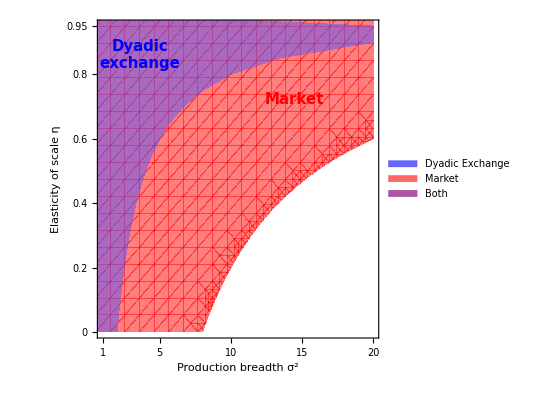

```mathematica
ptExchSpeTimeAlloc=Legended[Show[region2,region1,PlotRange->{{1,maxSigmaSquare},{0.,0.95}},AxesLabel->{"η","σ"},Frame->True,FrameLabel->{"Production breadth \!\(\*SuperscriptBox[\(σ\), \(2\)]\)","Elasticity of scale η"},LabelStyle->{Bold,14,Black},BaseStyle->{FontSize->18,Black},AspectRatio->1,PlotRangePadding->0,ImageSize->400,FrameTicks->{{{0,0.2,0.4,0.6,0.8,0.95},None},{{1,5,10,15,20},None}},Epilog->{Text[Style["Dyadic\nexchange",Bold,Blue,15],Scaled[{0.15,0.89}]],Text[Style["Market",Bold,Red,15],Scaled[{0.7,0.75}]]},Mesh->None],Placed[SwatchLegend[{Lighter[Blue,0.4],Lighter[Red,0.4],Lighter[Purple]},{"Dyadic Exchange","Market","Both"},LegendLayout->"Row",LegendMarkers->{"Square","Square","Square"},LabelStyle->{Bold,14},LegendMargins->50],Below]]
```

The second plot is a placeholder to replace using the plot done on R

```mathematica
ptExchSpeTimeAllocCombined=Grid[{{Style["Effect of emergence of exchange on",Bold,25,GrayLevel[0.2],FontFamily->"Palatino"],SpanFromLeft},{Labeled[ptExchSpeTimeAlloc,Column[{Style["Genetic Diversity",Bold,18,FontFamily->"Palatino"],Style["(Invasibility coefficient > 0)",Gray,Italic,12,FontFamily->"Palatino"]}],Top],Labeled[ptExchSpeTimeAlloc,Column[{Style["Economic Specialisation",Bold,18,FontFamily->"Palatino"],Style["(For dyadic exchange)",Gray,Italic,12,FontFamily->"Palatino"] }],Top]}},Spacings->{2,1},Frame->False,Mesh->None];
```

```mathematica
ptExchSpeTimeAllocSimple=Show[region2,PlotRange->{{0.5,maxSigmaSquare},{0.,0.95}},AxesLabel->{"η","σ"},Frame->True,ImageSize->Small,FrameLabel->{"Production breadth \!\(\*SuperscriptBox[\(σ\), \(2\)]\)","Elasticity of scale η"},LabelStyle->{Bold,10,Black}
,BaseStyle->{FontSize->14,Black},AspectRatio->0.8,PlotRangePadding->0,ImageSize->450,FrameTicks->{{None,None},{None,None}},Mesh->None];
```

```mathematica
ptExchSpeTimeAllocSimpleLegend=Legended[Show[region2,PlotRange->{{0.5,maxSigmaSquare},{0.,0.95}},AxesLabel->{"η","σ"},Frame->True,FrameLabel->{"Production breadth \!\(\*SuperscriptBox[\(σ\), \(2\)]\)","Elasticity of scale η"},LabelStyle->{Bold,10,Black},BaseStyle->{FontSize->14,Black},AspectRatio->0.8,PlotRangePadding->0,ImageSize->400,FrameTicks->{{None,None},{None,None}},Mesh->None],Placed[SwatchLegend[{Lighter[Blue,0.4],Lighter[Red,0.4],Lighter[Purple]},{"Dyadic Exchange","Market","Both"},LegendLayout->"Row",LegendMarkers->{"Square","Square","Square"},LabelStyle->{Bold,14}],Below]];
```

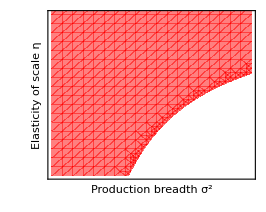
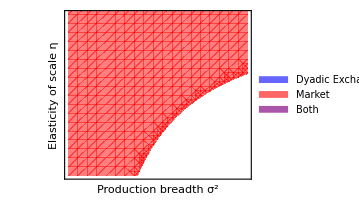
Effect of emergence of exchange on | 
-Graphics-Genetic Diversity
Genetic Diversity
(Uninvadibility coefficient > 0)

 | -Graphics-Economic Specialisation
With dyadic exchange
-Graphics-With market exchange

```mathematica
ptExchSpeTimeAllocCombined=Grid[{{Style["Effect of emergence of exchange on",Bold,25,GrayLevel[0.2],FontFamily->"Palatino"],SpanFromLeft},{Labeled[ptExchSpeTimeAlloc,Column[{Style["Genetic Diversity",Bold,18,FontFamily->"Palatino",White],Style["Genetic Diversity",Bold,18,FontFamily->"Palatino"],Style["(Uninvadibility coefficient > 0)",Gray,Italic,12,FontFamily->"Palatino"],,}],Top],Grid[{{Labeled[Show[ptExchSpeTimeAllocSimple,ImageSize->266],Column[{Style["Economic Specialisation",Bold,18,FontFamily->"Palatino"],Style["With dyadic exchange",Gray,14,Bold,FontFamily->"Palatino"]}],Top]},{Labeled[Show[ptExchSpeTimeAllocSimpleLegend,ImageSize->266],Column[{Style["With market exchange                    ",Gray,14,Bold,FontFamily->"Palatino"]}],Top]}}]}},Spacings->{2,1},Frame->False,Mesh->None]
```

```mathematica
SetDirectory[StringJoin[$HomeDirectory,"\\OneDrive\\Research\\A1-Projects\\2023_ExchPoly\\res\\Simul\\sweep"]];
Export["pt_exch_spe_time_alloc2.pdf",Rasterize[ptExchSpeTimeAllocCombined,ImageResolution->600]]
```

pt_exch_spe_time_alloc2.pdf

## Market exchange

For the case of market exchange, we derived analytically the price in a monomorphic population so we can conduct the evolutionary analysis analytically.

```mathematica
(*Remove assumptions applied globally*)
$Assumptions=True;
(*Set assumptions that can be used to simplify expressions*)
myAssumptions =  p>0 &&rx[τ]>0&&ry[τ]>0&&rx[θ]>0&&ry[θ]>0&&0<η<1 && 0 <α < 1  ;
SetOptions[Simplify,Assumptions->myAssumptions];
SetOptions[FullSimplify,Assumptions->myAssumptions];
(*Silence warnings from Solve about inverse functions*)
Off[Solve::ifun]
```

#### Utility and mutant payoff

```mathematica
(*Utility function*)
Π[cx_,cy_]:=cx^α cy^(1-α)
(*Invasion payoff of an individual τ in a resident monomorphic population  of trait θ*) 
paEconDiminishingMarket[τ_,θ_]:=Π[cx[τ,θ],cy[τ,θ]]
```

```mathematica
cx[τ_,θ_]:=α (qx[hx[τ,θ],τ]+ qy[1-hx[τ,θ],τ] 1/p[θ])
cy[τ_,θ_]:= (1-α)(p[θ] qx[hx[τ,θ],τ]+ qy[1-hx[τ,θ],τ])
p[θ_]:=(α/(1-α))^(1-η) ry[θ]/rx[θ];
```

```mathematica
qx[hx_,τ_]:=hx^η rx[τ]
qy[hy_,τ_]:=hy^η ry[τ]
```

```mathematica
hx[τ_,θ_]:=1/(1+(1-α)/α(rx[θ]/ry[θ] ry[τ]/rx[τ])^(1/(1-η)))
```

```mathematica
rx[z_]:=Exp[(-(z-ox)^2)/σ^2]
ry[z_]:=Exp[(-(z-oy)^2)/σ^2]
```

```mathematica
subs={α->0.5,ox->-2,oy->2}
```

{α→0.5,ox→-2,oy→2}

```mathematica
PowerExpand[Selec[paEconDiminishingMarket[τ,θ]]//FullSimplify];
Comp[%,(2 ⅇ^(-((α (ox-θ)^2+(1-α) (oy-θ)^2)/σ^2)) (1-α)^((1-α) η) α^(α η) (α ox + (1-α) oy-θ))/σ^2,"Selection gradient"]
(2 ⅇ^(-((α (ox-θ)^2+(1-α) (oy-θ)^2)/σ^2)) (1-α)^((1-α) η) α^(α η) (oy(1-α)+ox α-θ))/σ^2/.subs//FullSimplify
```

Selection gradient:

Selection gradient = (2 ⅇ^(-(α (ox-θ)^2+(1-α) (oy-θ)^2)/σ^2) (1-α)^((1-α) η) α^(α η) (α ox+(1-α) oy-θ))/σ^2

-(2 ⅇ^(-0.693147 η+(-4.-1. θ^2)/σ^2) θ)/σ^2

The payoff gradient is the same than in autarky

```mathematica
PowerExpand[SelecNoPrint[paEconDiminishingMarket[τ,θ]]//FullSimplify]==PowerExpand[SelecNoPrint[paNoEx[τ,θ]]//FullSimplify]//Simplify
```

True

```mathematica
Singular[paEconDiminishingMarket[τ,θ]]//Simplify
singularPtSub={θ->oy+ox α-oy α};
```

Singular point(s):

{θ→oy+ox α-oy α,θ→oy+σ (-∞),θ→oy+σ ∞,θ→ox+σ (-∞),θ→ox+σ ∞}

```mathematica
Synergy[paEconDiminishingMarket[τ,θ]]/.singularPtSub//Simplify;
Comp[%,-(4 (ⅇ^(-((ox-oy)^2 (1-α)^2)/σ^2))^α (ⅇ^(-((ox-oy)^2 α^2)/σ^2) (1-α)^η)^(1-α) (ox-oy)^2 (1-α) α^(1+α η))/((1-η) σ^4),"Synergy coefficient"]
```

Cross-derivative - Neg freq dependent selection:

Synergy coefficient = -(4 (ⅇ^(-((ox-oy)^2 (1-α)^2)/σ^2))^α (ⅇ^(-((ox-oy)^2 α^2)/σ^2) (1-α)^η)^(1-α) (ox-oy)^2 (1-α) α^(1+α η))/((1-η) σ^4)

```mathematica
PowerExpand[Invad[paEconDiminishingMarket[τ,θ]]/.singularPtSub]//Simplify;
Comp[%,(2 (ⅇ^(-((ox-oy)^2 α^2)/σ^2) (1-α)^η)^(1-α) (ⅇ^(-((ox-oy)^2 (1-α)^2)/σ^2) α^η)^α (2 (ox-oy)^2 (1-α) α-(1-η) σ^2))/((1-η) σ^4),"Uninvadibility coefficient"]
```

Heissian - Evolutionary stability:

Uninvadibility coefficient = (2 (ⅇ^(-((ox-oy)^2 α^2)/σ^2) (1-α)^η)^(1-α) (ⅇ^(-((ox-oy)^2 (1-α)^2)/σ^2) α^η)^α (2 (ox-oy)^2 (1-α) α-(1-η) σ^2))/((1-η) σ^4)

Rearranging the expression

```mathematica
2 (ox-oy)^2 (1-α) α-(1-η) σ^2>0;
HL[(ox-oy)^2/σ^2 > (1.-η)/(2 α (1-α)),"Label"->"Conditions for polymorphism "]
```

Conditions for polymorphism  = (ox-oy)^2/σ^2>(1.-η)/(2 (1-α) α)

For the same parameters specification than with dyadic exchange.

```mathematica
((ox-oy)^2/σ^2 > (1.-η)/(2 α (1-α)))/.subs
```

16/σ^2>2. (1.-η)

```mathematica
HL[σ^2 < 8/(1.-η),"Label"->"Conditions for polymorphism "]
```

Conditions for polymorphism  = σ^2<8/(1.-η)